```mathematica
ourFib[1] = 1; ourFib[2] = 1;
ourFib[n_] := ourFib[n - 1] + ourFib[n - 2]

phi = (1 + Sqrt[5])/2;
psi = (1 - Sqrt[5])/2;
fastFib[n_]:= FullSimplify[(phi^n - psi^n) / (phi - psi)]
```

```mathematica
table =TableForm[
Table[
{
n,
ourFib[n],
Timing[ourFib[n]][[1]],
fastFib[n],
Timing[fastFib[n]][[1]],
Fibonacci[n],
Timing[Fibonacci[n]][[1]]
},
{n, 1, 34}
],
TableHeadings->{None,{
"n",
"ourFib[n]",
"ourFib[] timing",
"fastFib[n]",
"fastFib[] timing",
"Fibonacci[n]",
"Fibonacci[] timing"}},
TableAlignments->Center
]
```

n | ourFib[n] | ourFib[] timing | fastFib[n] | fastFib[] timing | Fibonacci[n] | Fibonacci[] timing
1 | 1 | 0. | 1 | 0. | 1 | 0.
2 | 1 | 0. | 1 | 0. | 1 | 0.
3 | 2 | 0. | 2 | 0. | 2 | 0.
4 | 3 | 0. | 3 | 0. | 3 | 0.
5 | 5 | 0. | 5 | 0. | 5 | 0.
6 | 8 | 0. | 8 | 0. | 8 | 0.
7 | 13 | 0. | 13 | 0. | 13 | 0.
8 | 21 | 0. | 21 | 0. | 21 | 0.
9 | 34 | 0. | 34 | 0. | 34 | 0.
10 | 55 | 0. | 55 | 0. | 55 | 0.
11 | 89 | 0. | 89 | 0. | 89 | 0.
12 | 144 | 0. | 144 | 0. | 144 | 0.
13 | 233 | 0. | 233 | 0. | 233 | 0.
14 | 377 | 0. | 377 | 0. | 377 | 0.
15 | 610 | 0. | 610 | 0. | 610 | 0.
16 | 987 | 0. | 987 | 0. | 987 | 0.
17 | 1597 | 0. | 1597 | 0. | 1597 | 0.
18 | 2584 | 0. | 2584 | 0. | 2584 | 0.
19 | 4181 | 0.015625 | 4181 | 0. | 4181 | 0.
20 | 6765 | 0.015625 | 6765 | 0. | 6765 | 0.
21 | 10946 | 0.015625 | 10946 | 0. | 10946 | 0.
22 | 17711 | 0.015625 | 17711 | 0. | 17711 | 0.
23 | 28657 | 0.015625 | 28657 | 0. | 28657 | 0.
24 | 46368 | 0.03125 | 46368 | 0. | 46368 | 0.
25 | 75025 | 0.0625 | 75025 | 0. | 75025 | 0.
26 | 121393 | 0.078125 | 121393 | 0. | 121393 | 0.
27 | 196418 | 0.0625 | 196418 | 0. | 196418 | 0.
28 | 317811 | 0.21875 | 317811 | 0. | 317811 | 0.
29 | 514229 | 0.265625 | 514229 | 0. | 514229 | 0.
30 | 832040 | 0.453125 | 832040 | 0. | 832040 | 0.
31 | 1346269 | 0.859375 | 1346269 | 0. | 1346269 | 0.
32 | 2178309 | 1.48438 | 2178309 | 0. | 2178309 | 0.
33 | 3524578 | 2.32813 | 3524578 | 0. | 3524578 | 0.
34 | 5702887 | 3.5625 | 5702887 | 0. | 5702887 | 0.

```mathematica
Export["C:\\Users\\brijk\\OneDrive\\Desktop\\some homework\\table.pdf",table]
```

C:\Users\brijk\OneDrive\Desktop\some homework\table.pdf

```mathematica
F[x_]:=x/(1-x-x^2)
```

```mathematica
array =TableForm[
Table[
{n,
TraditionalForm@Simplify[D[F[x],{x,n}]],
(D[F[x],{x,n}]/.x->0)/n!
},
{n,0,11}
]
]
```

0 | -x/(x^2+x-1) | 0
1 | (x^2+1)/((x^2+x-1)^2) | 1
2 | -(2 (x^3+3 x+1))/((x^2+x-1)^3) | 1
3 | (6 (x^4+6 x^2+4 x+2))/((x^2+x-1)^4) | 2
4 | -(24 (x^5+10 x^3+10 x^2+10 x+3))/((x^2+x-1)^5) | 3
5 | (120 (x^6+15 x^4+20 x^3+30 x^2+18 x+5))/((x^2+x-1)^6) | 5
6 | -(720 (x^7+21 x^5+35 x^4+70 x^3+63 x^2+35 x+8))/((x^2+x-1)^7) | 8
7 | (5040 (x^8+28 x^6+56 x^5+140 x^4+168 x^3+140 x^2+64 x+13))/((x^2+x-1)^8) | 13
8 | -(40320 (x^9+36 x^7+84 x^6+252 x^5+378 x^4+420 x^3+288 x^2+117 x+21))/((x^2+x-1)^9) | 21
9 | (362880 (x^10+45 x^8+120 x^7+420 x^6+756 x^5+1050 x^4+960 x^3+585 x^2+210 x+34))/((x^2+x-1)^10) | 34
10 | -(3628800 (x^11+55 x^9+165 x^8+660 x^7+1386 x^6+2310 x^5+2640 x^4+2145 x^3+1155 x^2+374 x+55))/((x^2+x-1)^11) | 55
11 | (39916800 (x^12+66 x^10+220 x^9+990 x^8+2376 x^7+4620 x^6+6336 x^5+6435 x^4+4620 x^3+2244 x^2+660 x+89))/((x^2+x-1)^12) | 89

```mathematica
TeXForm[array]
```

\begin{array}{ccc}
 0 & -\frac{x}{x^2+x-1} & 0 \\
 1 & \frac{x^2+1}{\left(x^2+x-1\right)^2} & 1 \\
 2 & -\frac{2 \left(x^3+3
   x+1\right)}{\left(x^2+x-1\right)^3} & 1 \\
 3 & \frac{6 \left(x^4+6 x^2+4
   x+2\right)}{\left(x^2+x-1\right)^4} & 2 \\
 4 & -\frac{24 \left(x^5+10 x^3+10 x^2+10
   x+3\right)}{\left(x^2+x-1\right)^5} & 3 \\
 5 & \frac{120 \left(x^6+15 x^4+20 x^3+30 x^2+18
   x+5\right)}{\left(x^2+x-1\right)^6} & 5 \\
 6 & -\frac{720 \left(x^7+21 x^5+35 x^4+70 x^3+63
   x^2+35 x+8\right)}{\left(x^2+x-1\right)^7} & 8
   \\
 7 & \frac{5040 \left(x^8+28 x^6+56 x^5+140 x^4+168
   x^3+140 x^2+64
   x+13\right)}{\left(x^2+x-1\right)^8} & 13 \\
 8 & -\frac{40320 \left(x^9+36 x^7+84 x^6+252
   x^5+378 x^4+420 x^3+288 x^2+117
   x+21\right)}{\left(x^2+x-1\right)^9} & 21 \\
 9 & \frac{362880 \left(x^{10}+45 x^8+120 x^7+420
   x^6+756 x^5+1050 x^4+960 x^3+585 x^2+210
   x+34\right)}{\left(x^2+x-1\right)^{10}} & 34 \\
 10 & -\frac{3628800 \left(x^{11}+55 x^9+165
   x^8+660 x^7+1386 x^6+2310 x^5+2640 x^4+2145
   x^3+1155 x^2+374
   x+55\right)}{\left(x^2+x-1\right)^{11}} & 55 \\
 11 & \frac{39916800 \left(x^{12}+66 x^{10}+220
   x^9+990 x^8+2376 x^7+4620 x^6+6336 x^5+6435
   x^4+4620 x^3+2244 x^2+660
   x+89\right)}{\left(x^2+x-1\right)^{12}} & 89 \\
\end{array}

```mathematica
VA = Solve[Denominator@F[x]==0];
```

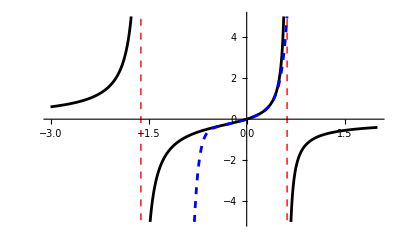

```mathematica
graph =Plot[
{F[x],
Evaluate@Normal@Series[F[x],{x,0,11}]},
{x,-3,2},
PlotRange->{{-3,2},{-5,5}},
PlotStyle->{{Black,Automatic},{Blue,Dashed}},
Epilog->{Dashed,Red,
InfiniteLine[{x,0},{0,1}]/.VA
}
]
```

```mathematica
Export["C:\\Users\\brijk\\OneDrive\\Desktop\\some homework\\graph.pdf",graph]
```

C:\Users\brijk\OneDrive\Desktop\some homework\graph.pdf